```mathematica
L=1.1;
h=1;
```

```mathematica
fexact[x_,y_]:=Cos[2 π(x+y^2)]/(1+x)
```

```mathematica
vexact[x_,y_]:={Cos[2 π x],Sin[2π x]}
```

```mathematica
texact[x_,y_]:={{Cos[2 π(x + 1.23 y)],Cos[4 π(x - y)]},{Sin[3 π (x+y/2)],Cos[2 π(x+y^2)]/(1+x)}}
```

```mathematica
f = Import ["/Users/michelecastellana/Desktop/f_sub_mesh.csv"]
```

```mathematica
v= Import ["/Users/michelecastellana/Documents/finite_elements/poisson_equation/solve_u/two_domains/solution/v_mesh.csv"]
```

```mathematica
t = Import ["/Users/michelecastellana/Desktop/t_sub_mesh.csv"]
```

```mathematica
(*read scalar field*)
```

```mathematica
tf=Table[{f[[i,2]],f[[i,1]]},{i,2,Length[t]}]
```

{{0.,1.},{0.037931,0.93622},{0.075862,0.82588},{0.11379,0.67795},{0.15172,0.50272},{0.18966,0.31113},{0.22759,0.11435},{0.26552,-0.076929},{0.30345,-0.25283},{0.34138,-0.4049},{0.37931,-0.52635},{0.41724,-0.61234},{0.45517,-0.66012},{0.4931,-0.66912},{0.53103,-0.64077},{0.56897,-0.57846},{0.6069,-0.48714},{0.64483,-0.37315},{0.68276,-0.24366},{0.72069,-0.10642}}

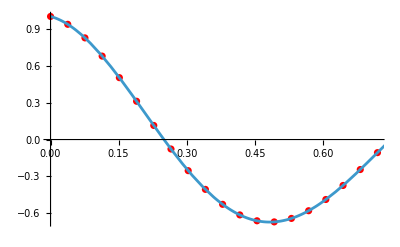

```mathematica
Show[ListPlot[tf,PlotStyle->Red],Plot[fexact[x,h],{x,0,L}]]
```

```mathematica
(*read vector field*)
```

```mathematica
ϵ=1*^-3;
For[tv={};i=1,i<=Length[v],i++,
If[Abs[v[[i,5]]-h]<ϵ,AppendTo[tv,{v[[i,4]],{v[[i,1]],v[[i,2]]}}]]
]
```

```mathematica
tv
```

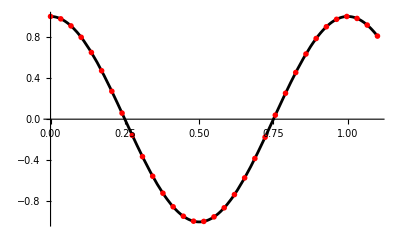

```mathematica
Show[Plot[vexact[x,h][[1]],{x,0,L},PlotStyle->Black],ListPlot[Table[{tv[[i,1]],tv[[i,2,1]]},{i,1,Length[tv]}],PlotStyle->{Red,PointSize->0.01}]]
```

```mathematica
(*read  tensor field*)
```

```mathematica
t11=Table[{t[[i,10]],t[[i,1]]},{i,2,Length[t]}]
```

{{0.,0.12533},{0.057895,-0.23586},{0.11579,-0.56619},{0.17368,-0.82241},{0.23158,-0.971},{0.28947,-0.99253},{0.34737,-0.88415},{0.40526,-0.66006},{0.46316,-0.3496},{0.52105,0.0066178},{0.57895,0.36196},{0.63684,0.66994},{0.69474,0.89025},{0.75263,0.99405},{0.81053,0.96776},{0.86842,0.81481},{0.92632,0.55523},{0.98421,0.22299},{1.0421,-0.13844},{1.1,-0.48175}}

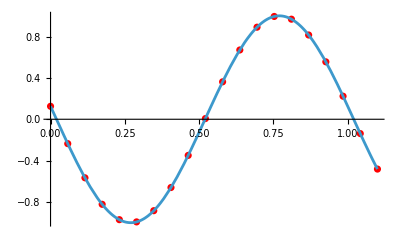

```mathematica
Show[ListPlot[t11,PlotStyle->Red],Plot[texact[x,h][[1,1]],{x,0,L}]]
```

```mathematica
t12=Table[{t[[i,10]],t[[i,2]]},{i,2,Length[t]}]
```

{{0.,1.},{0.057895,0.74672},{0.11579,0.11523},{0.17368,-0.57435},{0.23158,-0.97326},{0.28947,-0.87985},{0.34737,-0.34034},{0.40526,0.37157},{0.46316,0.89478},{0.52105,0.96523},{0.57895,0.54707},{0.63684,-0.14809},{0.69474,-0.76838},{0.75263,-0.99945},{0.81053,-0.72434},{0.86842,-0.082439},{0.92632,0.60105},{0.98421,0.98047},{1.0421,0.86331},{1.1,0.30902}}

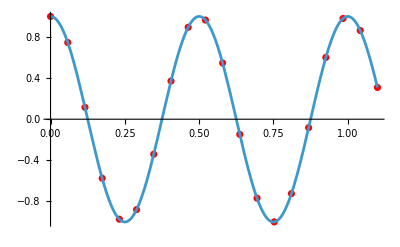

```mathematica
Show[ListPlot[t12,PlotStyle->Red],Plot[texact[x,h][[1,2]],{x,0,L}]]
```

```mathematica
t21=Table[{t[[i,10]],t[[i,4]]},{i,2,Length[t]}]
```

{{0.,-1.},{0.057895,-0.85477},{0.11579,-0.46129},{0.17368,0.066099},{0.23158,0.5743},{0.28947,0.91577},{0.34737,0.99127},{0.40526,0.77886},{0.46316,0.34025},{0.52105,-0.19715},{0.57895,-0.67727},{0.63684,-0.96074},{0.69474,-0.96527},{0.75263,-0.68934},{0.81053,-0.21322},{0.86842,0.32473},{0.92632,0.76839},{0.98421,0.98896},{1.0421,0.9223},{1.1,0.58779}}

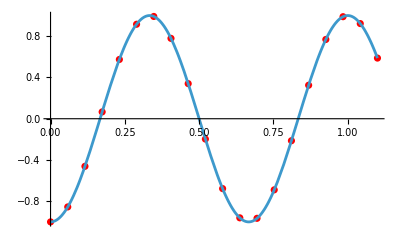

```mathematica
Show[ListPlot[t21,PlotStyle->Red],Plot[texact[x,h][[2,1]],{x,0,L}]]
```

```mathematica
t22=Table[{t[[i,10]],t[[i,5]]},{i,2,Length[t]}]
```

{{0.,1.},{0.057895,0.88342},{0.11579,0.66931},{0.17368,0.39307},{0.23158,0.093773},{0.28947,-0.19037},{0.34737,-0.42626},{0.40526,-0.58922},{0.46316,-0.66522},{0.52105,-0.6517},{0.57895,-0.557},{0.63684,-0.39869},{0.69474,-0.2008},{0.75263,0.0094345},{0.81053,0.20503},{0.86842,0.36249},{0.92632,0.46448},{0.98421,0.5015},{1.0421,0.47265},{1.1,0.38525}}

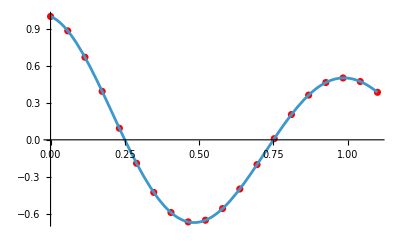

```mathematica
Show[ListPlot[t22,PlotStyle->Red],Plot[texact[x,h][[2,2]],{x,0,L}]]
```